# Markov Networks

Yang Long

#### Pairwise Markov Networks

A pairwise Markov network is an undirected graph whose nodes are X_1,..., X_n and each edge X_i-X_j is associated with a factor(potential) ϕ_ij(X_i-X_j).

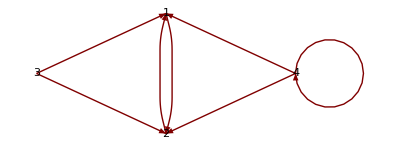

```mathematica
GraphPlot[{1->2,2->1,3->1,3->2,4->1,4->2,4->4},VertexLabeling->True,DirectedEdges->True]
```

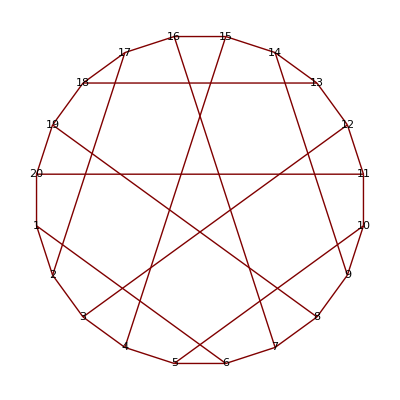

```mathematica
GraphPlot[GraphData["DesarguesGraph","EdgeRules"],VertexCoordinateRules->GraphData["DesarguesGraph","VertexCoordinateRules"],VertexLabeling->True]
```

#### General Gibbs Distribution

P(A,B,C,D)

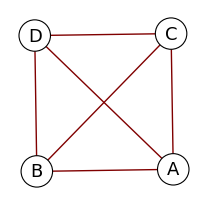

```mathematica
GraphPlot[{"A"->"B","B"->"C","C"->"D","D"->"A","A"->"C","B"->"D"},VertexLabeling->True,VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.1],Black,Text[Style[#2,18],#1]}&)]
```

Consider a fully connected pairwise Markov network over X_1,..., X_n where each X_i has d values. How many parameters does the network have? O(n^2 d^2)

O((n
2) d^2)=O((n(n-1))/2 d^2)=O(n^2 d^2)

Factors:

Φ={ϕ_1(D_1),...,ϕ_k(D_k)},   unnormalized measure ϕ_i

(P̃)_Φ(X_1,...,X_n)=(Π_(i=1))^k ϕ_i(D_i)

Z_Φ=∑_(X_1,...,X_n) (P̃)_Φ(X_1,....,X_n)

P_Φ(X_1,...,X_n)=1/Z_Φ(P̃)_Φ(X_1,...,X_n)

Gibbs Free energy will be the corresponding thing in physics to the gibbs distribution for random variables

##### Induced Markov Network

Induced Markov network H_Φ has an edge X_i-X_j whenever there exists ϕ_m∈Φ s.t. X_i,X_j∈ϕ_m.

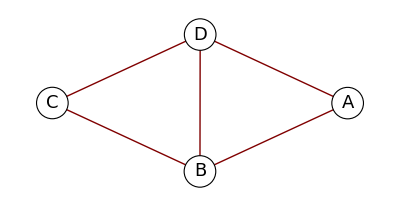

```mathematica
GraphPlot[{"A"->"B","B"->"C","C"->"D","D"->"A","B"->"D"},VertexLabeling->True,VertexRenderingFunction->({White,EdgeForm[Black],Disk[#,.1],Black,Text[Style[#2,18],#1]}&)]
```

All following Gibbs distribution would induce the above graph

ϕ_1(A,B,D), ϕ_2(B,C,D)
ϕ_1(A,B), ϕ_2(B,C), ϕ_3(C,D), ϕ_4(A,D), ϕ_5(B,D)
ϕ_1(A,B,D), ϕ_2(B,C), ϕ_3(C,D)

Influence can flow along any trail, regardless of the for m of the factors

A trail X_1-...-X_n is active given Z if no X_i is in Z.

#### Summary

Gibbs distribution represents distribution as a product of factors
Induced Markov network connects every pair of nodes that are in the same factor
Markov network structure doesn’t fully specify the factorization of P
But active trails depend only on graph structure